## Example to illustrate gain scheduling (Problem 11.2)

PI temperature control with nonlinearity from heater power:  P =V^2/R.

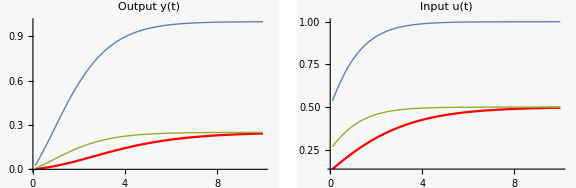

```mathematica
Clear["Global`*"];
tend=10;

(* Calculate for fixed PI gains *)
values0={kp->1/2, ki->1/2};
e[t]=r-y[t];  (* negative error term with nonlinear sensor *)
equations={y'[t]==- y[t]+ u[t]^2, u'[t]== ki e[t] - kp y'[t]}/.values0;
initialConditions={y[0]==0,u[0]==kp (r-y[0])}/.values0;

values1={r->1};
{y1,u1}=NDSolveValue[{equations,initialConditions}/.values1,{y,u},{t,0,tend}];

values2={r->0.25};
{y2,u2}=NDSolveValue[{equations,initialConditions}/.values2,{y,u},{t,0,tend}];


(* Redo with gain scheduling.  See at bottom for calculation of kp, ki. *)
values00={kp->1/(2 √r), ki->1/(2 √r)};
equations1={y'[t]==- y[t]+ u[t]^2, u'[t]== ki e[t] - kp y'[t]}/.values00;
initialConditions1={y[0]==0,u[0]==kp (r-y[0])}/.values00;
{y2a,u2a}=NDSolveValue[{equations1,initialConditions1}/.values2,{y,u},{t,0,tend}];


p1=Plot[{y1[t],y2[t],y2a[t]},{t,0.1,tend},PlotLabel->"Output y(t)",PlotRange->All,PlotStyle->{Thick,Red}];
p2=Plot[{u1[t],u2[t],u2a[t]},{t,0.1,tend},PlotLabel->"Input u(t)",PlotRange->All,PlotStyle->{Thick,Red}];
GraphicsRow[{p1,p2},ImageSize->Large]
```

Calculate the transfer function after linearization

```mathematica
a=({{-1, 2 √r}, {-ki, 0}});b=({{0}, {ki}});c=({{1, 0}}); einv=Inverse[({{1, 0}, {kp, 1}})];  
	(* linearization about y=r+dy, u=√r0+du, r=r+dr *)
sys=StateSpaceModel[{einv.a,einv.b,c}];
{tf=TransferFunctionModel[sys,s],einv.a//MatrixForm}
```

{(2 ki √r)/(2 ki √r+s+2 kp √r s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11221FalseFalseFalseAutomaticNoneAutomatic,(-1 | 2 √r
-ki+kp | -2 kp √r)}

Choose kp = ki = 1/(2 √r) to keep response the same:  tf =  1/(s+1)^2.

Export data

```mathematica
(* 
SetDirectory[NotebookDirectory[]];dt=0.01;y1t=Table[y1[[1]],{t,0,tend,dt}];  Export["GainSchedulingDat1.dat",y1t];
y2t=Table[y2[[1]],{t,0,tend,dt}];  Export["GainSchedulingDat2.dat",y2t];
y2at=Table[y2a[[1]],{t,0,tend,dt}];  Export["GainSchedulingDat2a.dat",y2at]; 
*)
```